## “Ray” trajectory in natural variables

Started 30/05/2015
Ignoring the diffusive term in the FPE within the wall, construct a geometrical picture of the trajectories taken by particles injected at η_0. The variables used here have been re-scaled: θ=η/β, ξ=x/β. This leaves us a one-parameter problem. See notes for more details.

#### Trajectory equation

```mathematica
Δξ[θ_,θ0_]:=Log[θ/θ0]-θ+θ0
```

#### Trajectory profile

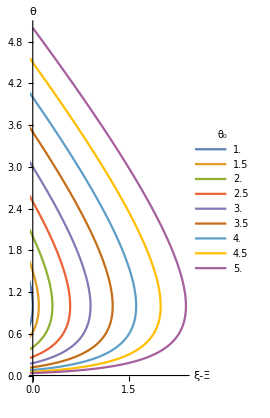

```mathematica
θ0m=5;
ParametricPlot[
Table[{Δξ[θ,θ0],θ},{θ0,1,θ0m,(θ0m-1)/8}]//Evaluate,
{θ,0,θ0m},PlotRange->{{0,Automatic},All},
AxesLabel->{"ξ-Ξ","θ"},
PlotLegends->LineLegend[Table[θ0,{θ0,1,θ0m,(θ0m-1)/8}]//N,LegendLabel->"θ_0"]]
```

#### Maximum distance from wall

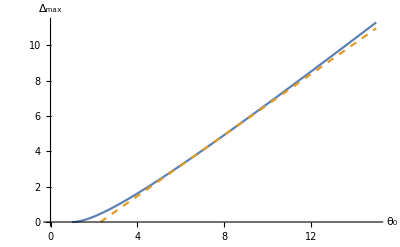

```mathematica
Plot[{Δξ[1,θ0],6.9/8(θ0-2.3)},
{θ0,1,15},
PlotStyle->{Full,Dashed},
PlotRange->{{0,Automatic},{0,Automatic}},
AxesLabel->{"θ_0","Δ_max"}]
```

#### Trajectory endpoint

```mathematica
θ1[θ0_]:=Re[
θ/.FindRoot[Δξ[θ,θ0]==0,{θ,1/θ0}]
]//Quiet
```

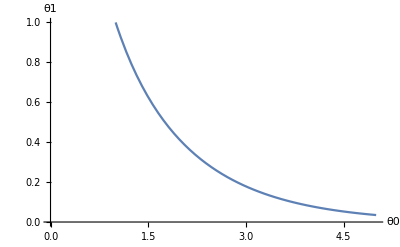

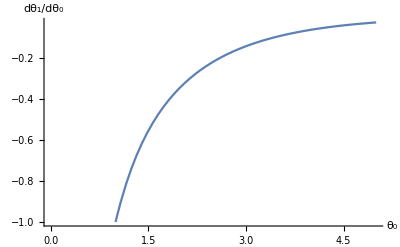

```mathematica
θ0m=5;
Plot[θ1[θ0],{θ0,1,θ0m},
PlotRange->{{0,θ0m},{0,1}},
AxesLabel->{"θ0","θ1"}]
Plot[(1-1/θ0)/(1-1/θ1[θ0]),{θ0,1,θ0m},
PlotRange->{{0,Automatic},All},
AxesLabel->{"θ_0","dθ_1/dθ_0"}]
```

#### Trajectory length

```mathematica
Σ[θ0_,θ_]:=Assuming[θ0≥1&&θ0>θ≥0,
-Integrate[√((1/θθ-1)^2+1),{θθ,θ0,θ}]]//Evaluate//Simplify
Σ[θ0,θ]
```

-√(1-2 θ+2 θ^2)+√(1-2 θ0+2 θ0^2)-ArcSinh[1-2 θ]/(√2)+ArcSinh[1-2 θ0]/(√2)-Log[(θ (1-θ0+√(1-2 θ0+2 θ0^2)))/((1-θ+√(1-2 θ+2 θ^2)) θ0)]

```mathematica
θ0m=30;
θ0list=Table[θ0,{θ0,1,θ0m,(θ0m-1)/30.0}]//N;
θ1list=θ1/@θ0list;
Σlist=Σ[θ0,θ1]/.{θ0->θ0list,θ1->θ1list};
Σplot=ListLinePlot[Transpose[{θ0list,Σlist}],
AxesLabel->{"θ_0","Σ(θ_0)"}];
```

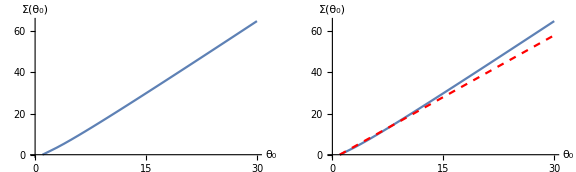

```mathematica
Show[{Σplot,Plot[2(θ0-1),{θ0,1,θ0m},PlotStyle->Directive[Red,Dashed]]}];
GraphicsRow[{Σplot,%},ImageSize->Large]
```

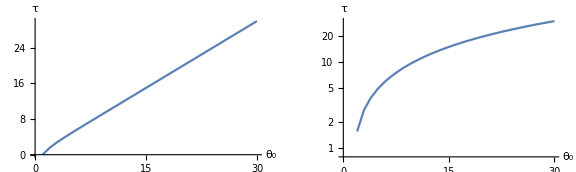

```mathematica
τ[R_]:=Log[R]
Rlist=θ0list/θ1list;
pltτ=ListLinePlot[Transpose[{θ0list,τ/@Rlist}],
AxesLabel->{"θ_0","τ"}]//Quiet;
pltlnτ=ListLogPlot[Transpose[{θ0list,τ/@Rlist}],
Joined->True,
AxesLabel->{"θ_0","τ"}]//Quiet;
GraphicsRow[{pltτ,pltlnτ},ImageSize->Large]
```

#### Trajectory duration

1.93856+0.434498 Σ

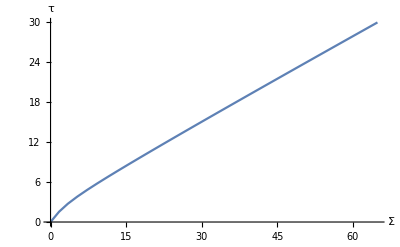

```mathematica
Σfit=Fit[Transpose[{Σlist[[5;;]],τ/@Rlist[[5;;]]}],{1,Σ},Σ]
Show[{ListLinePlot[Transpose[{Σlist,τ/@Rlist}],
AxesLabel->{"Σ","τ"}],
Plot[Σfit,{σ,0,65},PlotStyle->{Red,Dashed}]}]
```

#### Is diffusion important?

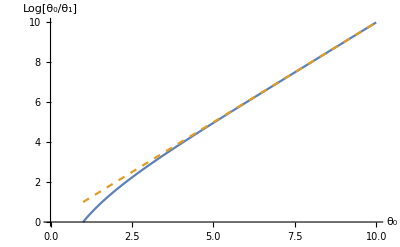

```mathematica
Plot[{Log[θ0/θ1[θ0]],θ0},
{θ0,1,10},
PlotRange->{{0,Automatic},Automatic},
PlotStyle->{Full,Dashed},
AxesLabel->{"θ_0","Log[θ_0/θ_1]"}]
```

#### Probability density given Gaussian at wall

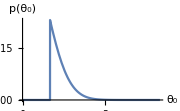

```mathematica
b=1.5;
p[θ0_,β_]:=√(β/(2π))Exp[-β/2 θ0^2]HeavisideTheta[θ0-1]
Plot[p[θ0,b],{θ0,0,5},
PlotRange->All,Exclusions->None,AxesLabel->{"θ_0","p(θ_0)"},ImageSize->Small]
```

```mathematica
θ0[θ_,Δ_]:=Re[θ0/.FindRoot[Δξ[θ,θ0]==Δ,{θ0,1+θ}]]//Quiet
(*ρl[θ_,θ0_,ρ0_]:=√((1-θ0)^2+θ0^2)θ0/(1-1/θ0)Abs[(1-1/θ)/(√(2 θ^2-2θ+1))]*ρ0 (* Subscript[δΔ, 0]=0 *)*)
ρa[θ_,θ0_,ρ0_]:=√((1-θ0)^2+θ0^2)θ0/(θ0-1)(θ-1)^2/(2 θ^2-2θ+1)*ρ0 (* Subscript[δΔ, 0]≠0 *)
```

```mathematica
ρau=Plot3D[ρa[θ,θ0[θ,δ],1],
{θ,0,2},{δ,0,2},
PlotRange->Automatic,
PlotLabel->"Uniform θ_0 (δΔ_0≠0)",AxesLabel->{"θ","Δ","ρ"}];
ρag=Plot3D[ρa[θ,θ0[θ,δ],p[θ0[θ,δ],b]],
{θ,0,2},{δ,0,0.5},
PlotRange->All,
PlotLabel->"Gaussian θ_0 (δΔ_0≠0)",AxesLabel->{"θ","Δ","ρ"}];
GraphicsRow[{ρau,ρag},ImageSize->Large]
```

-Graphics-

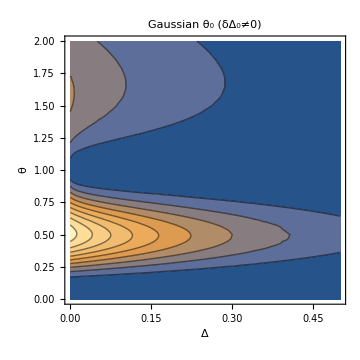

```mathematica
b=1;
ρagc=ContourPlot[ρa[θ,θ0[θ,δ],p[θ0[θ,δ],b]]//Re,
{δ,0,0.5},{θ,0,2},
PlotRange->All,
PlotLabel->"Gaussian θ_0 (δΔ_0≠0)",
FrameLabel->{"Δ","θ"},
ImageSize->Medium]
```